## Load Data and Settings

### Preamble

```mathematica
ClearAll["Global`*"];
$Version
SetDirectory[NotebookDirectory[]]
(*SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]*)
(*SetOptions[$FrontEnd,PrintingStyleEnvironment->"Working"]*)
```

12.2.0 for Microsoft Windows (64-bit) (December 12, 2020)

C:\Users\Miguel Quartin\Downloads\covid19-ifr-br-master-new\covid19-ifr-br-master

```mathematica
resultDIR="results";
headertf={"eta+","sigma-eta","IFR","sigma-ifr","fa","fs","fd","taud","s/fa","s/ifr","s/eta","s/fd","s/fs","Dt-tab","nd","ns","UF","pop"};
Quiet[CreateDirectory[resultDIR]]

v[n_]=Erf[n/Sqrt[2]];
n95=FindRoot[v[n]==0.95,{n,2}][[1,2]]

color=RGBColor[0.98,0.81,0.49];
adjust[gr_]:=Show[gr,Graphics[{EdgeForm[{Thickness[.005],Blend[{Red,color},.8]}],FaceForm[color],Polygon[Cases[gr,Rectangle[{x1_,y1_},{x2_,y2_},_]:>Sequence[{x1,y1},{x1,y2},{x2,y2},{x2,y1}],Infinity]//.{s___,a_,a_,e___}:>{s,e}]}]]
```

C:\Users\Miguel Quartin\Downloads\covid19-ifr-br-master-new\covid19-ifr-br-master\results

1.95996

### Run settings

```mathematica
run=999;
phase=3;
faval=2;(* 1 for mode, 2 for median *)
fpr=1.00;(* 0.05% or 1.00% *)
mintest=0;minant=0;

popAgesIBGEy=Import["tables/ibge-projecao-2020.csv"][[1]];
Dimensions[popAgesIBGE=Thread[{Table[{0,4}+i 5,{i,0,18}],popAgesIBGEy}]];
TableForm[Transpose@popAgesIBGE];
poptotBra=Total[popAgesIBGEy];
ages={{0,116},{0,29},{30,49},{50,69},{70,116}};(*https://en.wikipedia.org/wiki/List_of_the_verified_oldest_people*)
(* Brazilian 2020 IBGE fractions *)
fracAges=1.{poptotBra,Total[popAgesIBGEy[[;;6]]],Total[popAgesIBGEy[[7;;10]]],Total[popAgesIBGEy[[11;;14]]],Total[popAgesIBGEy[[15;;]]]}/poptotBra;

timeab=60; (* time after which no antibodies *)
tauSA=5.8;
DeltaT=2;sigmaDT=1;

AbsoluteFileName[mule="epirun.nb"]
Quiet[CreateDirectory[resultDIR<>"/run"<>ToString[run]]]
```

C:\Users\Miguel Quartin\Downloads\covid19-ifr-br-master-new\covid19-ifr-br-master\epirun.nb

C:\Users\Miguel Quartin\Downloads\covid19-ifr-br-master-new\covid19-ifr-br-master\results\run999

### EPICOVID

```mathematica
Dimensions[dataepicovid=Import["tables/Epicovid-fases-1-2-3-pop.csv"]]
headermigepi={"state","city","t1","t2","t3","c1","c2","c3","f1","f2","f3","p1","p2","p3","pop"};
TableForm[dataepicovid[[;;3]],TableHeadings->{None, headermigepi}];

datapainel=DateObject[{2020,7,1}];
Which[
phase==1
,
datei=DateObject[{2020,5,14}];
datem=DateObject[{2020,5,17}];
datef=DateObject[{2020,5,21}];
,
phase==2
,
datei=DateObject[{2020,6,4}];
datem=DateObject[{2020,6,5}];
datef=DateObject[{2020,6,7}];
,
phase==3||phase==0
,
datei=DateObject[{2020,6,21}];
datem=DateObject[{2020,6,22}];
datef=DateObject[{2020,6,24}];
];
headermig={"moda","mediana","pmin (95%)","pmax(95%)","cross-check de 95% entre pmin e pmax"};
(*Dimensions[datamigc=Import["tables/prob-tab-cities-FPR"<>ToString[NumberForm[fpr,{1,2}]]<>"%-round"<>ToString[phase]<>".csv"]]*)
Dimensions[datamigs=Import["tables/prob-tab-states-FPR"<>ToString[NumberForm[fpr,{1,2}]]<>"%-round"<>ToString[phase]<>"-v6a.csv"]]
Dimensions[datamigb=Import["tables/prob-tab-Brazil-FPR"<>ToString[NumberForm[fpr,{1,2}]]<>"%-round"<>ToString[phase]<>"-v6.csv"]]
Dimensions[stateso=Sort[DeleteDuplicates[dataepicovid[[All;;,1]]]]];
```

{133,15}

{27,8}

{1,8}

```mathematica
(* filtering *)
If[
mintest==0&&minant==0
,
Dimensions[cities=dataepicovid[[All;;,2]]];
Dimensions[states=Sort[DeleteDuplicates[dataepicovid[[All;;,1]]]]]
,
Dimensions[auxt=dataepicovid[[All,{2+phase,2+phase+3}]]];
Dimensions[pos200=Flatten[Position[auxt,_?((#[[1]]≥mintest&&#[[2]]≥minant)&)]]];
Dimensions[dataepicovid=dataepicovid[[pos200]]];
Dimensions[datamigc=datamigc[[pos200]]];

Dimensions[cities=dataepicovid[[All;;,2]]];
Dimensions[states=Sort[DeleteDuplicates[dataepicovid[[All;;,1]]]]];

comsta=Complement[stateso,states];
tabpo=Table[
Position[stateso,comsta[[i]]][[1,1]]
,{i,Length[comsta]}];
pobo=Complement[Range[Length[stateso]],tabpo];
Dimensions[datamigs=datamigs[[pobo]]];
];
```

```mathematica
TableForm[datamigb[[All]],TableHeadings->{{"Brasil"}, headermig}]
TableForm[datamigs[[All]],TableHeadings->{states, headermig}]
(*TableForm[datamigc[[All]],TableHeadings->{cities, headermig}];*)
TableForm[dataepicovid[[All]],TableHeadings->{None, headermigepi}];
```

| moda | mediana | pmin (95%) | pmax(95%) | cross-check de 95% entre pmin e pmax |  |  | 
Brasil | 0.0381 | 0.0382 | 0.0327 | 0.0439 | 0.95 | 292.813 | 5545.88 | 0.0029

| moda | mediana | pmin (95%) | pmax(95%) | cross-check de 95% entre pmin e pmax |  |  | 
AC | 0.049054949885968247548903738 | 0.05066983698172527878354924566722 | 0.02743329652496559305987005 | 0.076877281831311103908804982 | 0.94999999458948299644587141 | 23.0566 | 340.597 | 0.0127611
AL | 0.13099879654930944220406769 | 0.1327550682995847970669540179384 | 0.09275166328556404494331797 | 0.17596646854680899386695394 | 0.94999999272144508484090276 | 39.5916 | 232.408 | 0.0213441
AM | 0.074536629532436141206064622 | 0.07664685866715132315007432581552 | 0.044446800703253881944179776 | 0.11271361004086302537495584 | 0.94999999362836819144261819 | 23.5109 | 238.822 | 0.0176022
AP | 0.13176396272128128515237629 | 0.1339135965527914953339308875478 | 0.08970509842694447566444897 | 0.1820413210708496069972557 | 0.949999992530676093255712 | 32.6016 | 189.317 | 0.0237109
BA | 0.023077518574112928847131585 | 0.02434937665202938801501765796507 | 0.009097269624167384979743722 | 0.041950794245974287668490233 | 0.94999999630443328937290561 | 18.0544 | 471.065 | 0.0085155
CE | 0.1757855486267795781649952 | 0.1771509801564785019123233072038 | 0.13466473726283361060092921 | 0.22213090999753673189275912 | 0.9499999925753543835803868 | 58.0316 | 247.782 | 0.0223858
DF | 0. | 0.00602759153329318097571613577532 | 0 | 0.021582071798052442855433435 | 0.94999997219191315407793738 | 2.97556 | 206.907 | 0.0069229
ES | 0.026448638504219403392948023 | 0.02741944313714347605025896459475 | 0.013291331887867063824690881 | 0.043339580954969806862886344 | 0.94999999538452089200234842 | 25.3136 | 610.153 | 0.007752
GO | 0.009489305244315711824105317 | 0.01075013113332052309082497728576 | 0.000171194331476772511583483 | 0.022561807944576694418407835 | 0.94996780925706959952672418 | 13.2332 | 559.813 | 0.0060841
MA | 0.070505613038108226192127139 | 0.07157558090924120556992342672024 | 0.048903927171309902100662823 | 0.09621300499429324535112146 | 0.94999999373116850066768093 | 43.8194 | 477.589 | 0.0121388
MG | 0.006285742205713743521365644 | 0.00666063195751589052422967309399 | 0.000982423623797910195157854 | 0.01284430463871317425090772 | 0.94999999480677611950757095 | 34.8411 | 1824.63 | 0.0030865
MS | 0.00492426615201714271419508 | 0.00633590865347089917426651883137 | 0. | 0.015258232013847730025339605 | 0.94999999796651675067800702 | 13.4241 | 725.588 | 0.0044571
MT | 0.006079110517953272747638902 | 0.00686588288115541794795883899351 | 0. | 0.014497930941312146852449131 | 0.94999999998730657701655537 | 19.7954 | 1025.68 | 0.0040018
PA | 0.062845483340921410587919102 | 0.0636790914143496280832896360463 | 0.044656341644437534243233022 | 0.084234736461736042751894 | 0.94999999384589411569427872 | 51.7922 | 629.442 | 0.0101472
PB | 0.016658391665305310682451002 | 0.01788072272263120021058892792515 | 0.004544725923830954642247305 | 0.033422986806092439149387762 | 0.94999999421362917200885541 | 15.7835 | 503.276 | 0.0075123
PE | 0.006404045353323789950147262 | 0.00819280743859670977592327856543 | 0. | 0.019656125271571291110201114 | 0.94999999934891168761686295 | 10.4577 | 507.307 | 0.0057189
PI | 0.080907047922949831025772978 | 0.08240488060314183065698599361029 | 0.053878525315935940356885919 | 0.11367834832988547020272369 | 0.94999999350804174913802389 | 34.559 | 328.911 | 0.0153646
PR | 0.007882746589839891102386 | 0.0082558624139017000746943244621 | 0.002074015071179648951476499 | 0.015075572693324571325553417 | 0.9499999925455993854282277 | 35.7395 | 1719.37 | 0.0033503
RJ | 0.079185695406750805291699585 | 0.08127563695482261621795511362925 | 0.048224784920004049543656911 | 0.11815426104541672777726993 | 0.9499999934889861844397487 | 24.6806 | 237.206 | 0.0180195
RN | 0.048779931963743032099662973 | 0.05041163989572474067307539264922 | 0.027120669864820468426670357 | 0.076704556870120536031215112 | 0.94999999460765171434548507 | 22.744 | 337.4 | 0.0127994
RO | 0.052889608119949203787750312 | 0.05501044216787649641032850743577 | 0.027667333915047113873445648 | 0.086251404155747619146451572 | 0.94999999462743773769990682 | 18.6799 | 256.063 | 0.0151594
RR | 0.20492499777121184258024494 | 0.206621547249514454395962543874 | 0.15420715121111264677622313 | 0.26212302652017567076593132 | 0.94999999219973635910970571 | 49.0075 | 174.37 | 0.0276273
RS | 0.004620458774715778797647842 | 0.00493319898609950321641204528902 | 0.000353168950255725411186992 | 0.009759250003186538822093588 | 0.9499999956581558855063585 | 42.4008 | 2460.61 | 0.0024865
SC | 0.005900792422377363560457454 | 0.0061627076008401671205768342245 | 0.00131653004515896148583299 | 0.011416553509381370332131807 | 0.94999999975780956380437444 | 46.9387 | 2530.97 | 0.0026037
SE | 0.026590945158653259112477272 | 0.02897732969393797051408004420536 | 0.007465340644238712857445847 | 0.054861202188268085459511645 | 0.94999999668188570484834198 | 10.9344 | 248.942 | 0.0124176
SP | 0.00694807351330496840776938 | 0.00869893205707821576144340301349 | 0. | 0.020506559558945225112236962 | 0.94999999909933585752065504 | 10.494 | 494.335 | 0.0059236
TO | 0.012142983329028584955347247 | 0.01283982439235214838563939121484 | 0.003522071529734974367230901 | 0.023407395831853998204871342 | 0.94999999330476458330187645 | 23.0963 | 896.669 | 0.0051421

### SIVEP-Gripe

```mathematica
(*AbsoluteTiming[Dimensions[datasivep3=Import["SIVEP-Gripe/INFLUD-23-11-2020c.csv",{"CSV","Data"},"Numeric"->True,"EmptyField"-> "XXXX",CharacterEncoding -> "UTF8"]]]*)
AbsoluteTiming[Dimensions[datasivep3=Import["SIVEP-Gripe/INFLUD-23-11-2020ca.csv"]]]
header=datasivep3[[1]];header6=header;
dateformat3={"Day","Month","Year"};
datasivep3=datasivep3[[2;;]];

dtNOT3=Position[header,s_String/;ToUpperCase[s]=="DT_NOTIFIC"][[1,1]];
dtSIN3=Position[header,s_String/;ToUpperCase[s]=="DT_SIN_PRI"][[1,1]];
dtINT3=Position[header,s_String/;ToUpperCase[s]=="DT_INTERNA"][[1,1]];
dtEVO3=Position[header,s_String/;ToUpperCase[s]=="DT_EVOLUCA"][[1,1]];
EVO3=Position[header,s_String/;ToUpperCase[s]=="EVOLUCAO"][[1,1]];
hosp3=Position[header,s_String/;ToUpperCase[s]=="HOSPITAL"][[1,1]];
corona3=Position[header,s_String/;ToUpperCase[s]=="PCR_SARS2"][[1,1]];
resUF3=Position[header,s_String/;ToUpperCase[s]=="SG_UF"][[1,1]];
resMUN3=Position[header,s_String/;ToUpperCase[s]=="CO_MUN_RES"][[1,1]];
resMUNname3=Position[header,s_String/;ToUpperCase[s]=="ID_MN_RESI"][[1,1]];
raca3=Position[header,s_String/;ToUpperCase[s]=="CS_RACA"][[1,1]];
dtUTI3=Position[header,s_String/;ToUpperCase[s]=="DT_ENTUTI"][[1,1]];
UTI3=Position[header,s_String/;ToUpperCase[s]=="UTI"][[1,1]];
dtNAS3=Position[header,s_String/;ToUpperCase[s]=="DT_NASC"][[1,1]];
IDADE3=Position[header,s_String/;ToUpperCase[s]=="NU_IDADE_N"][[1,1]];

TableForm[datasivep3[[-5;;]],TableHeadings->{None, header}]
```

{38.631,{369238,154}}

DT_NOTIFIC | SEM_NOT | DT_SIN_PRI | SEM_PRI | SG_UF_NOT | ID_REGIONA | CO_REGIONA | ID_MUNICIP | CO_MUN_NOT | ID_UNIDADE | CO_UNI_NOT | CS_SEXO | DT_NASC | NU_IDADE_N | TP_IDADE | COD_IDADE | CS_GESTANT | CS_RACA | CS_ETINIA | CS_ESCOL_N | ID_PAIS | CO_PAIS | SG_UF | ID_RG_RESI | CO_RG_RESI | ID_MN_RESI | CO_MUN_RES | CS_ZONA | SURTO_SG | NOSOCOMIAL | AVE_SUINO | FEBRE | TOSSE | GARGANTA | DISPNEIA | DESC_RESP | SATURACAO | DIARREIA | VOMITO | OUTRO_SIN | OUTRO_DES | PUERPERA | FATOR_RISC | CARDIOPATI | HEMATOLOGI | SIND_DOWN | HEPATICA | ASMA | DIABETES | NEUROLOGIC | PNEUMOPATI | IMUNODEPRE | RENAL | OBESIDADE | OBES_IMC | OUT_MORBI | MORB_DESC | VACINA | DT_UT_DOSE | MAE_VAC | DT_VAC_MAE | M_AMAMENTA | DT_DOSEUNI | DT_1_DOSE | DT_2_DOSE | ANTIVIRAL | TP_ANTIVIR | OUT_ANTIV | DT_ANTIVIR | HOSPITAL | DT_INTERNA | SG_UF_INTE | ID_RG_INTE | CO_RG_INTE | ID_MN_INTE | CO_MU_INTE | UTI | DT_ENTUTI | DT_SAIDUTI | SUPORT_VEN | RAIOX_RES | RAIOX_OUT | DT_RAIOX | AMOSTRA | DT_COLETA | TP_AMOSTRA | OUT_AMOST | PCR_RESUL | DT_PCR | POS_PCRFLU | TP_FLU_PCR | PCR_FLUASU | FLUASU_OUT | PCR_FLUBLI | FLUBLI_OUT | POS_PCROUT | PCR_VSR | PCR_PARA1 | PCR_PARA2 | PCR_PARA3 | PCR_PARA4 | PCR_ADENO | PCR_METAP | PCR_BOCA | PCR_RINO | PCR_OUTRO | DS_PCR_OUT | CLASSI_FIN | CLASSI_OUT | CRITERIO | EVOLUCAO | DT_EVOLUCA | DT_ENCERRA | DT_DIGITA | HISTO_VGM | PAIS_VGM | CO_PS_VGM | LO_PS_VGM | DT_VGM | DT_RT_VGM | PCR_SARS2 | PAC_COCBO | PAC_DSCBO | OUT_ANIM | DOR_ABD | FADIGA | PERD_OLFT | PERD_PALA | TOMO_RES | TOMO_OUT | DT_TOMO | TP_TES_AN | DT_RES_AN | RES_AN | POS_AN_FLU | TP_FLU_AN | POS_AN_OUT | AN_SARS2 | AN_VSR | AN_PARA1 | AN_PARA2 | AN_PARA3 | AN_ADENO | AN_OUTRO | DS_AN_OUT | TP_AM_SOR | SOR_OUT | DT_CO_SOR | TP_SOR | OUT_SOR | DT_RES | RES_IGG | RES_IGM | RES_IGA
10/11/2020 | 46 | 27/10/2020 | 44 | DF | XXXX | XXXX | BRASILIA | 530010 | HOSPITAL SANTA LUZIA | 3005402 | M | 01/07/1961 | 59 | 3 | 3059 | 6 | 4 | XXXX | 9 | BRASIL | 1 | DF | XXXX | XXXX | VICENTE PIRES | 539934 | 1 | 9 | 9 | 9 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | XXXX | XXXX | S | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 9 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 2 | XXXX | XXXX | XXXX | 1 | 09/11/2020 | DF | XXXX | XXXX | BRASILIA | 530010 | 1 | 09/11/2020 | XXXX | 3 | 6 | XXXX | XXXX | 1 | 30/10/2020 | 1 | XXXX | 1 | 31/10/2020 | 2 | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 5 | XXXX | 1 | 1 | 17/11/2020 | 18/11/2020 | 11/11/2020 | 9 | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | XXXX | XXXX | XXXX | 2 | 2 | 2 | 2 | 1 | XXXX | 09/11/2020 | XXXX | XXXX | 5 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX
15/11/2020 | 47 | 06/11/2020 | 45 | SP | GVE XV BAURU | 1340 | BAURU | 350600 | HOSPITAL BENEFICENCIA PORTUGUESA DE BAURU | 3003361 | M | 31/12/1987 | 32 | 3 | 3032 | 6 | 1 | XXXX | 4 | BRASIL | 1 | SP | GVE XV BAURU | 1340 | BAURU | 350600 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | XXXX | 2 | S | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | XXXX | 1 | OBESIDADE | 1 | 15/07/2020 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | 1 | XXXX | 06/11/2020 | 1 | 15/11/2020 | SP | GVE XV BAURU | 1340 | BAURU | 350600 | 2 | XXXX | XXXX | 2 | 6 | XXXX | XXXX | 1 | 11/11/2020 | 1 | XXXX | 1 | 14/11/2020 | 2 | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 5 | XXXX | 1 | XXXX | XXXX | XXXX | 18/11/2020 | 0 | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | XXXX | XXXX | XXXX | 2 | 2 | 2 | 2 | 1 | XXXX | 14/11/2020 | XXXX | XXXX | 4 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX
09/11/2020 | 46 | 30/10/2020 | 44 | MG | POUSO ALEGRE | 1459 | ITAJUBA | 313240 | AISI HOSPITAL DE CLINICAS DE ITAJUBA | 2208857 | F | 27/04/1934 | 86 | 3 | 3086 | 5 | 1 | XXXX | 3 | BRASIL | 1 | MG | POUSO ALEGRE | 1459 | ITAJUBA | 313240 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | PROSTRACAO | 1 | S | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | XXXX | 2 | XXXX | 1 | 24/05/2020 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | 1 | XXXX | 31/10/2020 | 1 | 07/11/2020 | MG | POUSO ALEGRE | 1459 | ITAJUBA | 313240 | 1 | 07/11/2020 | XXXX | 2 | 6 | XXXX | XXXX | 1 | 02/11/2020 | 1 | XXXX | 1 | 04/11/2020 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 5 | XXXX | 1 | XXXX | XXXX | XXXX | 20/11/2020 | 2 | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | 513210 | COZINHEIRO DO SERVICO DOMESTICO | XXXX | 2 | 2 | 2 | 2 | 6 | XXXX | XXXX | XXXX | XXXX | 5 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 4 | 4 | 4
14/11/2020 | 46 | 12/11/2020 | 46 | SP | GVE I CAPITAL | 1331 | SAO PAULO | 355030 | HOSPITAL DO CORACAO | 2081288 | F | 12/03/1932 | 88 | 3 | 3088 | 5 | 9 | XXXX | XXXX | BRASIL | 1 | SP | GVE X OSASCO | 1335 | BARUERI | 350570 | 1 | 2 | 2 | 2 | XXXX | 1 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | CEFALEIA; DOR RETROESTERNAL | XXXX | S | 1 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | 14/11/2020 | SP | XXXX | XXXX | SAO PAULO | 355030 | 1 | 14/11/2020 | XXXX | 2 | XXXX | XXXX | XXXX | 1 | 14/11/2020 | 1 | XXXX | 1 | 14/11/2020 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 5 | XXXX | XXXX | XXXX | XXXX | XXXX | 20/11/2020 | 2 | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | XXXX | XXXX | XXXX | XXXX | 1 | XXXX | XXXX | 1 | XXXX | 14/11/2020 | XXXX | XXXX | 5 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX
30/10/2020 | 44 | 25/10/2020 | 44 | PA | 01 REGIONAL DE PROTECAO SOCIAL | 1484 | BELEM | 150140 | HOSPITAL PORTO DIAS | 2332809 | F | 03/02/1965 | 55 | 3 | 3055 | 5 | 4 | XXXX | 4 | BRASIL | 1 | PA | 01 REGIONAL DE PROTECAO SOCIAL | 1484 | ANANINDEUA | 150080 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | ASTENIA E MAL ESTAR | 2 | S | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | XXXX | 2 | XXXX | 2 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 2 | XXXX | XXXX | XXXX | 1 | 30/10/2020 | PA | 01 REGIONAL DE PROTECAO SOCIAL | 1484 | BELEM | 150140 | 2 | XXXX | XXXX | 3 | 6 | XXXX | XXXX | 1 | 31/10/2020 | 1 | XXXX | 1 | 04/11/2020 | 2 | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | 5 | XXXX | 1 | 1 | 04/11/2020 | 20/11/2020 | 20/11/2020 | 2 | XXXX | XXXX | XXXX | XXXX | XXXX | 1 | XXXX | XXXX | XXXX | 2 | 2 | 2 | 2 | 6 | XXXX | XXXX | XXXX | XXXX | 4 | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX | XXXX

```mathematica
(* covid cases *)
(*AbsoluteTiming@Dimensions[datasivep3=Select[datasivep3,(#[[corona3]]==1)&]]
Export["SIVEP-Gripe/INFLUD-23-11-2020ca.csv",datasivep3,"TableHeadings"->header6]*)
```

```mathematica
(*TableForm[Select[datasivep3,(#[[IDADE3]]>115)&],TableHeadings->{None, header6}]*)
```

### Painel Coronavírus

```mathematica
(* 25/02/20 -> 2020-02-25 *)
```

```mathematica
PCfun:=(
(*AbsoluteTiming[Dimensions[datasaude=Import["painel/HIST_PAINEL_COVIDBR_17jul2020.csv","CSV"]]];*)
AbsoluteTiming[Dimensions[datasaude=Import["painel/HIST_PAINEL_COVIDBR_27nov2020.csv","CSV"]]];
(*dateformatPC={"Day","Month","YearShort"};*)
dateformatPC={"Year","Month","Day"};
header=datasaude[[1]];
datasaude=datasaude[[2;;]];

ufPa=Position[header,"estado"][[1,1]];
munPa=Position[header,"municipio"][[1,1]];
codPa=Position[header,"codmun"][[1,1]];
dtPa=Position[header,"data"][[1,1]];
popPa=Position[header,"populacaoTCU2019"][[1,1]];
posAPa=Position[header,"casosAcumulado"][[1,1]];
posPa=Position[header,"casosNovos"][[1,1]];
obAPa=Position[header,"obitosAcumulado"][[1,1]];
obPa=Position[header,"obitosNovos"][[1,1]];

TableForm[datasaude[[-5;;]],TableHeadings->{None, header}]
);

(*AbsoluteTiming[If[ageBin==1,PCfun]]*)
AbsoluteTiming[PCfun]
```

{16.8762,regiao | estado | municipio | coduf | codmun | codRegiaoSaude | nomeRegiaoSaude | data | semanaEpi | populacaoTCU2019 | casosAcumulado | casosNovos | obitosAcumulado | obitosNovos | Recuperadosnovos | emAcompanhamentoNovos | interior/metropolitana
Centro-Oeste | DF | Brasília | 53 | 530010 | 53001 | DISTRITO FEDERAL | 2020-11-23 | 48 | 3015268 | 224517 | 859 | 3882 | 15 |  |  | 1
Centro-Oeste | DF | Brasília | 53 | 530010 | 53001 | DISTRITO FEDERAL | 2020-11-24 | 48 | 3015268 | 225013 | 496 | 3898 | 16 |  |  | 1
Centro-Oeste | DF | Brasília | 53 | 530010 | 53001 | DISTRITO FEDERAL | 2020-11-25 | 48 | 3015268 | 225873 | 860 | 3906 | 8 |  |  | 1
Centro-Oeste | DF | Brasília | 53 | 530010 | 53001 | DISTRITO FEDERAL | 2020-11-26 | 48 | 3015268 | 226697 | 824 | 3910 | 4 |  |  | 1
Centro-Oeste | DF | Brasília | 53 | 530010 | 53001 | DISTRITO FEDERAL | 2020-11-27 | 48 | 3015268 | 227581 | 884 | 3915 | 5 |  |  | 1}

```mathematica
(*AbsoluteTiming[Dimensions[datasivep2=ImportString[StringReplace[Import["SIVEP-Gripe/INFLUD20-09102020.csv","Text"],{","->".",";"->","}],{"CSV","Data"},"Numeric"->True,"EmptyField"-> "XXXX",CharacterEncoding -> "UTF8"]]]*)
```

```mathematica
(*dateformat={"Day","Month","YearShort"};
Dimensions[datatest=Select[datasivep2,(#[[corona]]==1&&DateObjectQ[DateObject[{#[[dtEVO]],dateformat}]])&]]
MinMax[DateObject[{#,dateformat}]&/@datatest[[All,dtEVO]]]*)
```

## Run Brazil or States or Cities

### run Brazil

```mathematica
alevel=1; (* 1 for Brazil, 2 for state, 3 for city *)
If[alevel==1,blevel=1];

ndType=2; (* 1 for nd using Painel Coronavírus, 2 for SIVEP-Gripe3 *)
If[ndType==1,ageBin=1];(* there is no age info in Painel Coronavírus *)
```

```mathematica
(*ageBin=2;(* 1-5 *)
{ages[[ageBin]],fracAges[[ageBin]]}*)
```

```mathematica
AbsoluteTiming@Dimensions[tabfoda=Table[
ageBin=abe;(* 1-5 *)
Print[{ages[[ageBin]],fracAges[[ageBin]]}];
NotebookEvaluate[AbsoluteFileName[mule],InsertResults->False];
Join[vecfoda,{Length[Deltat],ndtot,"-"(*nstot*)}]
,{blevel,1},{abe,1,1(*5*)}]]
```

{{0,116},1.}

...running Brazil

{469.074,{1,1,16}}

```mathematica
(*AbsoluteTiming@Dimensions[tabfoda=Table[
NotebookEvaluate[AbsoluteFileName[mule],InsertResults->False];
Join[vecfoda,{Length[Deltat],ndtot,"-"(*nstot*)}]
,{blevel,1}]]*)
```

```mathematica
tabfoda=N[tabfoda];
tf=TableForm[tabfoda[[1]],TableHeadings->{Table["Brazil - age: "<>ToString[ages[[abe]]],{abe,1,5}],headertf}]
Export["results/run"<>ToString[run]<>"/"<>ToString[run]<>"-ztab-a"<>ToString[alevel]<>"-m"<>ToString[faval]<>"-f"<>ToString[phase]<>"_AgeBin"<>ToString[ageBin]<>".pdf",tf]
Export["results/run"<>ToString[run]<>"/"<>ToString[run]<>"-ztab-a"<>ToString[alevel]<>"-m"<>ToString[faval]<>"-f"<>ToString[phase]<>"_AgeBin"<>ToString[ageBin]<>".txt",Transpose@Join[{{"Brazil"}},Transpose[tabfoda]],"CSV","TableHeadings"->{headertf}]
```

| eta+ | sigma-eta | IFR | sigma-ifr | fa | fs | fd | taud | s/fa | s/ifr | s/eta | s/fd | s/fs | Dt-tab | nd | ns
Brazil - age: {0, 116} | - | - | 0.0105061 | 0.000804441 | 0.0382 | 0. | 0.000401331 | 15. | 0.0759162 | 0.0765693 | - | 0.00997931 | - | 29661. | 29962. | -

results/run999/999-ztab-a1-m2-f3_AgeBin1.pdf

results/run999/999-ztab-a1-m2-f3_AgeBin1.txt

### run state

```mathematica
alevel=2; (* 1 for Brazil, 2 for state, 3 for city *)
(*blevel=5;*) (* 1..27 if states, 1..133 if city *)
btab=Range[Length[datamigs]];
ndType=2; ageBin=1;(* 1-5 *)
{ages[[ageBin]],fracAges[[ageBin]]}
```

```mathematica
AbsoluteTiming@Dimensions[tabfoda=Table[
NotebookEvaluate[AbsoluteFileName[mule],InsertResults->False];
Join[vecfoda,{Length[Deltat],ndtot,"-"(*nstot*)}]
,{blevel,btab}]]
```

```mathematica
tabfoda=N[tabfoda];
tf=TableForm[tabfoda,TableHeadings->{states,headertf}]
Export["results/run"<>ToString[run]<>"/"<>ToString[run]<>"-ztab-a"<>ToString[alevel]<>"-m"<>ToString[faval]<>"-f"<>ToString[phase]<>".pdf",tf]
Export["results/run"<>ToString[run]<>"/"<>ToString[run]<>"-ztab-a"<>ToString[alevel]<>"-m"<>ToString[faval]<>"-f"<>ToString[phase]<>".txt",Transpose@Join[{states},Transpose[tabfoda]],"CSV","TableHeadings"->{headertf}]
```

### run city

```mathematica
(*alevel=3; (* 1 for Brazil, 2 for state, 3 for city *)
(*blevel=5;*) (* 1..27 if states, 1..133 if city *)
btab=Range[Length[datamigc]];
(* 1 to restrict to city's state, 0 to use city-only data, noisy  *)
stateonly=1;*)
```

```mathematica
(*AbsoluteTiming@Dimensions[tabfoda=Table[
NotebookEvaluate[AbsoluteFileName[mule],InsertResults->False];
Join[vecfoda,{Length[Deltat],ndtot,"-"(*nstot*),dataepicovid[[blevel,1]],dataepicovid[[blevel,-1]]}]
,{blevel,btab}]]*)
```

```mathematica
(*tabfoda=N[tabfoda];
tf=TableForm[tabfoda,TableHeadings->{cities,headertf}]
Export["results/run"<>ToString[run]<>"/"<>ToString[run]<>"-ztab-a"<>ToString[alevel]<>"-m"<>ToString[faval]<>"-f"<>ToString[phase]<>".pdf",tf]
Export["results/run"<>ToString[run]<>"/"<>ToString[run]<>"-ztab-a"<>ToString[alevel]<>"-m"<>ToString[faval]<>"-f"<>ToString[phase]<>".txt",Transpose@Join[{cities},Transpose[tabfoda]],"CSV","TableHeadings"->{headertf}]*)
```

## Plots

### plots paper

#### contagion to symptoms

```mathematica
{tauCS,sigmaCS}={Mean[LogNormalDistribution[1.621,0.418]],StandardDeviation[LogNormalDistribution[1.621,0.418]]}

Plot[PDF[LogNormalDistribution[1.621,0.418],t],{t,0,15},Frame->True,FrameStyle->14,FrameLabel->{"days",None},AspectRatio->1/2,PlotRange->{All,{0,All}},Filling->Bottom]
```

#### antibodies

```mathematica
Dimensions[abr=Import["nature-igg+igm-days-after.csv","CSV"]]
abr=abr[[3;;-2]];(* Vale ϵ^3 QC *)
abr[[{1,-1}]]
abrFODA=Join[{{-1,0},{0,0}(*,{2,0}*)},abr,{{25,100},{26,100}}];
iabr=Interpolation[abrFODA,InterpolationOrder->1]
```

```mathematica
(*tauA=FindRoot[iabr[t]==50,{t,5}][[1,2]]
{q1=FindRoot[iabr[t]==25,{t,2,.1,6}][[1,2]],q3=FindRoot[iabr[t]==75,{t,8.6,4,20}][[1,2]]}
sigmaA=q3-q1*)
```

```mathematica
abplo=ListLinePlot[abr,Frame->True,FrameStyle->14,FrameLabel->{"days after symptoms onset","positive rate [%]"},AspectRatio->1/2,PlotRange->{{All,20},All},Filling->Bottom]
(*Export["epilatex/figs/igg-igm.pdf",abplo]*)

abplo=Plot[iabr[t],{t,0,15},Frame->True,FrameStyle->14,FrameLabel->{"days after symptoms onset","positive rate [%]"},AspectRatio->1/2,PlotRange->{All,All},Filling->Bottom(*,GridLines->{{tauA,q1,q3}, {25,50,75}}*)]
(*Export["epilatex/figs/igg-igm.pdf",abplo]*)
```

```mathematica
tauSA=NIntegrate[1-iabr[x]/100,{x,0,26},Method->{Automatic,"SymbolicProcessing"->0}]
```

```mathematica
model=100Tanh[a t^b];
ff=FindFit[abrFODA[[3;;]],model,{{a,.1},{b,1.1}},t]
iabrFit[t_]=model/.ff;

Plot[{iabr[t],iabrFit[t]},{t,0,25},Frame->True,FrameStyle->14,FrameLabel->{"days after symptoms onset","positive rate [%]"},AspectRatio->1/2,PlotRange->{All,All},Filling->Bottom]

PDFabr[t_]:=iabr'[t]/100;
PDFabrFit[t_]:=iabrFit'[t]/100;
Plot[{PDFabr[t],PDFabrFit[t]},{t,0,25},Frame->True,FrameStyle->14,FrameLabel->{"days after symptoms onset","positive rate [%]"},AspectRatio->1/2,PlotRange->{All,{0,All}},Filling->Bottom]
```

```mathematica
{tauSAfit=NIntegrate[x PDFabrFit[x],{x,0,Infinity}],tauSA}
```

```mathematica
(*NIntegrate[PDFabrFit[x],{x,0,Infinity}]
PDFfi=ProbabilityDistribution[PDFabrFit[x],{x,0,Infinity}];
{tauA,sigmaA}={Median[PDFfi],InterquartileRange[PDFfi]}*)
```

```mathematica
(*tauA=NIntegrate[x PDFabrFit[x],{x,0,Infinity}]
sigmaA=NIntegrate[(x-tauA)^2 PDFabrFit[x],{x,0,Infinity}]^.5*)
```

```mathematica
(*{tauS,sigmaS}={(*Median[LogNormalDistribution[1.621,0.418]]*)5.1,InterquartileRange[LogNormalDistribution[1.621,0.418]]}*)
```

```mathematica
PDFabrC[t_]:=NIntegrate[PDFabrFit[x]PDF[LogNormalDistribution[1.621,0.418],t-x],{x,0,t},Method->{Automatic,"SymbolicProcessing"->0}];
(*PDFabrCx[t_]:=NIntegrate[PDFabrFit[t-x]PDF[LogNormalDistribution[1.621,0.418],x],{x,0,t},Method->{Automatic,"SymbolicProcessing"->0}];*)CDFabrC[tt_]:=NIntegrate[PDFabrC[y],{y,0,tt},Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
(*{{PDFabrC[10],PDFabrCx[10]},{PDFabrC[2],PDFabrCx[2]}}*)
```

```mathematica
(*NIntegrate[PDFabrC[z],{z,0,Infinity}]
PDFxxx=ProbabilityDistribution[PDFabrC[z],{z,0,Infinity}];*)
(*{tauX,sigmaX}={Median[PDFxxx],InterquartileRange[PDFxxx]}*)
```

```mathematica
{tauCA=NIntegrate[z PDFabrC[z],{z,0,100}],tauCS+tauSA}
```

```mathematica
(*{tauS+tauA,NIntegrate[PDFabrC[z],{z,0,tauS+tauA}]}
{meee=Median[LogNormalDistribution[1.621,0.418]]+tauA,NIntegrate[PDFabrC[z],{z,0,meee+tauA}]}
tauAS=FindRoot[NIntegrate[PDFabrC[z],{z,0,tt}]==.5,{tt,10}][[1,2]]
{q1=FindRoot[NIntegrate[PDFabrC[z],{z,0,tt}]==.25,{tt,10}][[1,2]],q3=FindRoot[NIntegrate[PDFabrC[z],{z,0,tt}]==.75,{tt,10}][[1,2]]}
sigmaAS=q3-q1*)
```

```mathematica
(*Plot[{PDFabrFit[t-tauS],PDFabrC[t]},{t,0,25},Frame->True,FrameStyle->14,FrameLabel->{"days after contagion","positive rate [%]"},AspectRatio->1/2,PlotRange->{All,{0,All}},Filling->Bottom,PlotPoints->10]*)
```

```mathematica
(*Plot[{iabr[t-tauS],100CDFabrC[t]},{t,0,25},Frame->True,FrameStyle->14,FrameLabel->{"days after contagion","positive rate [%]"},AspectRatio->1/2,PlotRange->{All,{0,All}},Filling->Bottom,PlotPoints->10]*)
```

```mathematica
(*iabF[t_]:=NIntegrate[iabr[t-x](*logns[x,mu,si,bi]*)PDF[LogNormalDistribution[1.621,0.418],x],{x,0,Infinity},Method->{Automatic,"SymbolicProcessing"->0}];*)
```

```mathematica
(*abplo=Plot[iabF[t],{t,0,30},Frame->True,FrameStyle->14,FrameLabel->{"days after contagion","positive rate [%]"},AspectRatio->1/2,PlotRange->{All,{0,All}},Filling->Bottom]*)
(*Export["epilatex/figs/igg-igm-cony.pdf",abplo]*)
```

```mathematica
abplo=Plot[{CDFabrC[t],(*iabr[t-tauS],*)HeavisideTheta[t-tauCA](*,100HeavisideTheta[t-tauAS]*)},{t,0,30},Frame->True,FrameStyle->14,Exclusions->False,FrameLabel->{"days",None},AspectRatio->1/2,(*PlotPoints->10,MaxRecursion->0,*)PlotRange->{All,{-.05,All}},PlotLegends->Placed[{Text[Style["f_ca(t)",Italic,FontSize->15]],Text[Style["H(t-τ_ca)",Italic,FontSize->15]]}(*{"f_ca(t)","H(t-τ_ca)"}*),{Scaled[{.65,0.5}], {0, 0.5}}]]
(*Export["epilatex/figs/igg-igm-cony.pdf",abplo]*)
```

```mathematica
(*AppendTo[tabpa=Table[{t,CDFabrC[t]},{t,0,29,1}],{30,1}]
Export["results/pa-tab.txt",tabpa,"Table"]*)
```

#### tausd sivep

```mathematica
(*Dimensions[datacovidx=datasivep]
AbsoluteTiming@Dimensions[datacovid=Select[datacovidx,(#[[corona]]==1&&#[[hosp]]==1&&#[[dtSIN]]≠"XXXX"&&DateObjectQ[DateObject[{#[[dtSIN]],dateformat}]]&&#[[dtINT]]≠"XXXX"&&DateObjectQ[DateObject[{#[[dtINT]],dateformat}]]&&(AbsoluteTime[DateObject[{#[[dtINT]],dateformat}]]-AbsoluteTime[DateObject[{#[[dtSIN]],dateformat}]]≥(*>*)0)&&#[[EVO]]==2&&#[[dtEVO]]≠"XXXX"&&DateObjectQ[DateObject[{#[[dtEVO]],dateformat}]]&&(AbsoluteTime[DateObject[{#[[dtEVO]],dateformat}]]-AbsoluteTime[DateObject[{#[[dtINT]],dateformat}]]≥0))&]]*)
```

```mathematica
(*AbsoluteTiming[Dimensions[Deltat=(DateDifference[DateObject[{#[[dtSIN]],dateformat}],DateObject[{#[[dtEVO]],dateformat}],"Days"]&/@datacovid)]]*)
{Mean[Deltat],StandardDeviation[Deltat]}
vecc={Median[Deltat],InterquartileRange[Deltat]}
```

```mathematica
Mean[Deltat][[1]]-tauSA
```

```mathematica
MinMax[Deltat]
hfoda=Histogram[Deltat,{1},Frame->True,PlotRange->{{All,40},All},FrameStyle->14(*,ChartBaseStyle->EdgeForm[None]*),FrameLabel->{{None,None},{"days",None}},PlotRangeClipping->True,AspectRatio->1/2,Epilog->{Text[Style["df_sd^sivep/dt",Italic,FontSize->15,TextAlignment->Left],Scaled[{.75,.7}]]}];
hfoda2=adjust[hfoda]
Export["epilatex/figs/tausd-sivep.pdf",hfoda2]
```

```mathematica
fsd=SmoothKernelDistribution[QuantityMagnitude[Deltat],MaxExtraBandwidths->0]
fcd[t_]:=NIntegrate[PDF[fsd,x]PDF[LogNormalDistribution[1.621,0.418],t-x],{x,0,t},Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
Plot[fcd[t],{t,0,60},Frame->True,FrameStyle->14,FrameLabel->{"days after contagion",None},AspectRatio->1/2,PlotRange->{All,{0,All}},Filling->Bottom,PlotPoints->10]
```

```mathematica
tauCD=NIntegrate[z fcd[z],{z,0,200},Method->{Automatic,"SymbolicProcessing"->0}]
Mean[LogNormalDistribution[1.621,0.418]]+Mean[Deltat][[1]]
```

```mathematica
FindRoot[NIntegrate[fcd[z],{z,0,tt},Method->{Automatic,"SymbolicProcessing"->0}] == 0.5,{tt,20}]
```

#### other taus

```mathematica
AbsoluteTiming[Dimensions[Deltas=(DateDifference[DateObject[{#[[dtSIN3]],dateformat3}],DateObject[{#[[dtINT3]],dateformat3}],"Days"]&/@datacovid3TauSD)]]
{Mean[Deltas],StandardDeviation[Deltas]}
{Median[Deltas],InterquartileRange[Deltas]}
```

```mathematica
MinMax[Deltas]
hfoda=Histogram[Deltas,{1},Frame->True,PlotRange->{{All,40},All},FrameStyle->14,FrameLabel->{"days"},PlotRangeClipping->True,AspectRatio->1/2,Epilog->{Text[Style["df_sh^sivep/dt",Italic,FontSize->15,TextAlignment->Left],Scaled[{.75,.7}]]}];
hfoda2=adjust[hfoda]
Export["epilatex/figs/taush-sivep.pdf",hfoda2]
```

```mathematica
AbsoluteTiming[Dimensions[Deltah=(DateDifference[DateObject[{#[[dtINT3]],dateformat3}],DateObject[{#[[dtEVO3]],dateformat3}],"Days"]&/@datacovid3TauSD)]]
{Mean[Deltah],StandardDeviation[Deltah]}
{Median[Deltah],InterquartileRange[Deltah]}
```

```mathematica
MinMax[Deltah]
hfoda=Histogram[Deltah,{1},Frame->True,PlotRange->{{All,40},All},FrameStyle->14,FrameLabel->{"days"},PlotRangeClipping->True,AspectRatio->1/2,Epilog->{Text[Style["df_hd^sivep/dt",Italic,FontSize->15,TextAlignment->Left],Scaled[{.75,.7}]]}];
hfoda2=adjust[hfoda]
Export["epilatex/figs/tauhd-sivep.pdf",hfoda2]
```

#### nd

```mathematica
(* identifying cities *)
Dimensions[citiesIBGE=Import["tables/Lista-de-Municípios-com-IBGE-Brasil.csv"]];

Dimensions[tabIBGE=Table[Flatten[Select[citiesIBGE,(StringMatchQ[#[[3]],dataepicovid[[bb,2]],IgnoreCase->True]&&#[[2]]==dataepicovid[[bb,1]])&]],{bb,Length[dataepicovid]}]];
Dimensions[tabIBGE=tabIBGE[[All,1]]]
```

{133}

```mathematica
selentry={8,10,11,12,13,14};
selentry2={11,12,13,14};
header[[selentry]]

Dimensions[tabPa=Table[
Select[datasaude,(#[[codPa]]==tabIBGE[[i]])&]
,{i,Length[tabIBGE]}]];

If[Length[DeleteDuplicates[tabPa[[All,1,8]]]]>1,Print[Row[{"Error in Painel C. - Brazil"}]]];

Dimensions[datasaudeF=tabPa[[1,All,selentry]]];
Dimensions[datasaudeF[[All,3;;]]=Total[tabPa[[All,All,selentry2]],{1}]];
Dimensions[datasaudeF]

TableForm[datasaudeF[[-10;;]],TableHeadings->{None, header[[selentry]]}]
```

{data,populacaoTCU2019,casosAcumulado,casosNovos,obitosAcumulado,obitosNovos}

{246,6}

data | populacaoTCU2019 | casosAcumulado | casosNovos | obitosAcumulado | obitosNovos
2020-11-18 | 88376 | 2502188 | 13398 | 82251 | 377
2020-11-19 | 88376 | 2516891 | 14703 | 82470 | 219
2020-11-20 | 88376 | 2532428 | 15537 | 82737 | 267
2020-11-21 | 88376 | 2545369 | 12941 | 82906 | 169
2020-11-22 | 88376 | 2552961 | 7592 | 82986 | 80
2020-11-23 | 88376 | 2561017 | 8056 | 83138 | 152
2020-11-24 | 88376 | 2572361 | 11344 | 83445 | 307
2020-11-25 | 88376 | 2590264 | 17903 | 83715 | 270
2020-11-26 | 88376 | 2604156 | 13892 | 84025 | 310
2020-11-27 | 88376 | 2616845 | 12689 | 84237 | 212

```mathematica
(*Dimensions[datasaudeF=Select[datasaude,(#[[ufPa]]=="")&]]*)
Dimensions[obData=Table[{DateObject[{datasaudeF[[i,1]],dateformatPC}],datasaudeF[[i,-1]]},{i,Length[datasaudeF]}]];
datei1=DateObject[{2020,5,14}];
datef1=DateObject[{2020,5,21}];
datei2=DateObject[{2020,6,4}];
datef2=DateObject[{2020,6,7}];
datei3=DateObject[{2020,6,21}];
datef3=DateObject[{2020,6,24}];
```

```mathematica
(*dbin=15;
Dimensions[obDataS=Table[{obData[[i+(dbin-1)/2,1]],Mean[obData[[Range[i,i+dbin-1],2]]]},{i,1,Length[obData]-(dbin-1),1(*dbin*)}]]*)
```

```mathematica
dbin=20;
Dimensions[obDataS=Table[{obData[[i,1]],Mean[obData[[Range[i,i+dbin-1],2]]]},{i,1,Length[obData]-(dbin-1),1(*dbin*)}]]
dapo=DateListStepPlot[obDataS,Frame->True,FrameStyle->14,PlotRangeClipping->True,AspectRatio->1/2,(*GridLines->{{datei,datef}, None},GridLinesStyle->Directive[Blue,Thickness[.005],Dashed],Method->{"GridLinesInFront"->True},*)PlotRange->{{DateObject[{2020,4,1}],datapainel},{0,All}},Epilog->{Text[Style["dn_d/dt",FontSize->15,Italic,TextAlignment->Left],Scaled[{.25,.7}]],EdgeForm[None],Opacity[.2],Blue,Rectangle[{datei1,0},{datef1,10000}],Rectangle[{datei2,0},{datef2,10000}],Rectangle[{datei3,0},{datef3,10000}]},Filling->Bottom,FrameLabel->{{None,None},{Automatic,None}}]
(*Export["epilatex/figs/dnd.pdf",dapo]*)
```

#### nd paper

```mathematica
PlotfunNdPaper[ob_,dbin_,lbl_,exp_,cor_]:=(
Dimensions[obDataS=Table[{ob[[i,1]],Mean[ob[[Range[i,i+dbin-1],2]]]},{i,1,Length[ob]-(dbin-1),1(*dbin*)}]];
dapo=DateListStepPlot[obDataS,Frame->True,FrameStyle->22,PlotRangeClipping->True,AspectRatio->1/2,(*GridLines->{{datei,datef}, None},GridLinesStyle->Directive[Blue,Thickness[.005],Dashed],Method->{"GridLinesInFront"->True},*)PlotRange->{{DateObject[{2020,4,1}],datapainel},{0,All}},PlotStyle->cor,PlotLegends->Placed[{Style[lbl,22]},Above],Epilog->{Text[Style["dn_d/dt",FontSize->22,Italic,TextAlignment->Left],Scaled[{.15,.7}]],EdgeForm[None],Opacity[.2],Blue,Rectangle[{datei1,0},{datef1,10000}],Rectangle[{datei2,0},{datef2,10000}],Rectangle[{datei3,0},{datef3,10000}]},Filling->Bottom,FrameLabel->{{None,None},{Automatic,None}}];
(*Export["epilatex/figs/dnd-new.pdf",dapo];*)
dapo
);
```

```mathematica
plabelndSG3="SIVEP-Gripe";
datei1=DateObject[{2020,5,14}];
datef1=DateObject[{2020,5,21}];
datei2=DateObject[{2020,6,4}];
datef2=DateObject[{2020,6,7}];
datei3=DateObject[{2020,6,21}];
datef3=DateObject[{2020,6,24}];
```

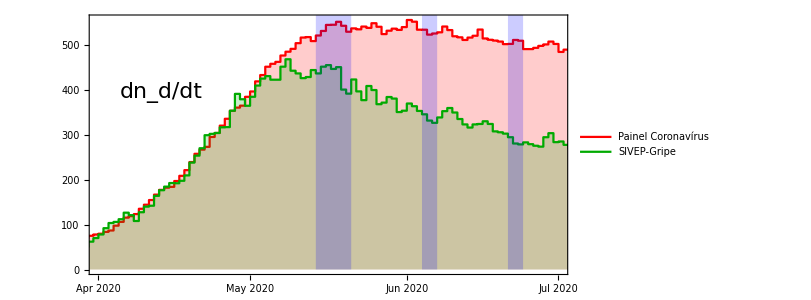

```mathematica
dapoPC=PlotfunNdPaper[obDataPC,dbinPC,plabelndPC,expoPC,Red];
(*dapoSG=PlotfunNd[obDataSG,dbinSG,plabelndSG,expoSG,Blue];*)
(*dapoSG2=PlotfunNd[obDataSG2,dbinSG2,plabelndSG2,expoSG2,Purple];*)
dapoSG3=PlotfunNdPaper[obDataSG3,dbinSG3,plabelndSG3,expoSG3,Darker[Green]];
dapo3=Show[dapoPC(*,dapoSG*)(*,dapoSG2*),dapoSG3,ImageSize->600]
Export["results/run"<>ToString[run]<>"/"<>ToString[run]<>"-nd.pdf",dapo3];
```

```mathematica
dapoPC=PlotfunNdPaper[obDataPC,dbinPC,plabelndPC,expoPC,Red];
obDataSexp=obDataS;
obDataSexp[[All,1]]=Map[AbsoluteTime,obDataS[[All,1]]];
obDataSexp[[All,2]]=1.obDataSexp[[All,2]];Export["fig-4S-Painel.csv",obDataSexp,"CSV"]
```

fig-4S-Painel.csv

```mathematica
dapoSG3=PlotfunNdPaper[obDataSG3,dbinSG3,plabelndSG3,expoSG3,Darker[Green]];
obDataSexp=obDataS;
obDataSexp[[All,1]]=Map[AbsoluteTime,obDataS[[All,1]]];
obDataSexp[[All,2]]=1.obDataSexp[[All,2]];
Export["fig-4S-SIVEP.csv",obDataSexp,"CSV"]
```

fig-4S-SIVEP.csv

#### mega tab UFs

```mathematica
run=503;
(*phase=1;*)
faval=2;(* 1 for mode, 2 for median *)
alevel=2; 
roo=.01;
df=2;
```

```mathematica
Do[tab[i]=Import["results/run"<>ToString[run]<>"/"<>ToString[run]<>"-ztab-a"<>ToString[alevel]<>"-m"<>ToString[faval]<>"-f"<>ToString[i]<>".txt","CSV","HeaderLines"->1,CharacterEncoding-> "UTF8"];
,{i,3}]
```

```mathematica
it=2;multi=1000;
fmz[tab_,it_]:=ToString[NumberForm[multi tab[[it,8]],df]]<>" ("<>ToString[NumberForm[Max[0.,multi(tab[[it,8]]-n95 tab[[it,13]]tab[[it,8]])],df]]<>"-"<>ToString[NumberForm[multi(tab[[it,8]]+n95 tab[[it,13]]tab[[it,8]]),df]]<>")";

tab[1][[it]]
fmz[tab[1],it]
```

```mathematica
Dimensions[tabM1=Import["tables/IFR-95CI-MQ-round1-40-80days-v6a.txt","CSV"]]
tabM1[[All,2;;]]=Round[100tabM1[[All,2;;]],roo];
Dimensions[tabM2=Import["tables/IFR-95CI-MQ-round2-40-80days-v6a.txt","CSV"]]
tabM2[[All,2;;]]=Round[100tabM2[[All,2;;]],roo];
Dimensions[tabM3=Import["tables/IFR-95CI-MQ-round3-40-80days-v6a.txt","CSV"]]
tabM3[[All,2;;]]=Round[100tabM3[[All,2;;]],roo];
Dimensions[tabMall=Import["tables/IFR-95CI-MQ-combined-40-80days-v6a.txt","CSV"]]
tabMall[[All,2;;]]=Round[100tabMall[[All,2;;]],roo];

TableForm[tabM1,TableHeadings->{None, {"UF","moda","mediana","95-","95+","check"}}]
```

```mathematica
Dimensions[tabP1=Import["tables/prob-tab-states-FPR1.00%-round1-v6a.csv","CSV"]]
tabP1=Round[100tabP1,roo];
Dimensions[tabP2=Import["tables/prob-tab-states-FPR1.00%-round2-v6a.csv","CSV"]]
tabP2=Round[100tabP2,roo];
Dimensions[tabP3=Import["tables/prob-tab-states-FPR1.00%-round3-v6a.csv","CSV"]]
tabP3=Round[100tabP3,roo];
(*Dimensions[tabPall=Import["tables/prob-tab-states-FPR1.00%-combined-v5.csv","CSV"]]*)
TableForm[tabP1,TableHeadings->{states, headermig}]
```

```mathematica
it=2;
fax[tab_,it_]:=ToString[NumberForm[tab[[it,1]],df]]<>" ("<>ToString[NumberForm[tab[[it,3]],df]]<>"-"<>ToString[NumberForm[tab[[it,4]],df]]<>")";
fmx[tab_,it_]:=ToString[NumberForm[tab[[it,2]],df]]<>" ("<>ToString[NumberForm[tab[[it,4]],df]]<>"-"<>ToString[NumberForm[tab[[it,5]],df]]<>")";

tabM1[[it]]
fmx[tabM1,it]

tabP1[[it]]
fax[tabP1,it]
```

```mathematica
Dimensions[megatab=Table[{Style[states[[i]],Bold],fax[tabP1,i],fax[tabP2,i],fax[tabP3,i],fmz[tab[1],i],fmz[tab[2],i],fmz[tab[3],i],fmx[tabM1,i],fmx[tabM2,i],fmx[tabM3,i],fmx[tabMall,i]},{i,Length[states]}]]
```

```mathematica
headgr={"State","p_a R1 (%)","p_a R2 (%)","p_a R3 (%)","p_d R1 (‰)","p_d R2 (‰)","p_d R3 (‰)","IFR R1 (%)","IFR R2 (%)","IFR R3 (%)","IFR all rounds (%)"};
headgr=Style[#,Bold]&/@ headgr;
tf=Grid[Join[{headgr},megatab],Dividers->Center,Spacings->{1,2},Alignment->{Center,Center}];
(*Export["results/run"<>ToString[run]<>"/"<>ToString[run]<>"-zmegatabG-a"<>ToString[alevel]<>"-m"<>ToString[faval]<>".pdf",tf]*)
```

```mathematica
tf=TableForm[megatab,TableHeadings->{None, headgr},TableSpacing->{3,1},TableAlignments->Center]
Export["results/run"<>ToString[run]<>"/"<>ToString[run]<>"-zmegatab-a"<>ToString[alevel]<>"-m"<>ToString[faval]<>".pdf",tf]
Export["results/run"<>ToString[run]<>"/"<>ToString[run]<>"-zmegatab-a"<>ToString[alevel]<>"-m"<>ToString[faval]<>".png",tf,ImageResolution->300]
```

```mathematica
(*Dimensions[megatabT=Transpose[megatab]]
tf=TableForm[megatabT,TableHeadings->{{"State","p_a R1 (%)","p_a R2 (%)","p_a R3 (%)","p_d R1 (‰)","p_d R2 (‰)","p_d R3 (‰)","IFR R1 (%)","IFR R2 (%)","IFR R3 (%)","IFR all rounds (%)"}, None}]
Export["results/run"<>ToString[run]<>"/"<>ToString[run]<>"-zmegatabT-a"<>ToString[alevel]<>"-m"<>ToString[faval]<>".pdf",tf]*)
```